# Notebook: Genetic diversity in facultatively sexual populations and its implications for the origins of self-incompatibility in algae, ciliates and fungi

## Analytic results from paper for Figures 4-8

```mathematica
Clear[πsAsex,πdAsex,πTotAsex]
```

```mathematica
σμTrans={σ->σB*NT,μ->μB*NT};

Clear[m]
(* In following σB = σBar = σ/N, μB = μBar = μ/N *)

πsAsex=k/(k+μ);
πdAsex=0;
πTotAsex=1/k k/(k+μ);

πTotUnisex=1/(1+μ);
ϕUnisex=μ/(1+μ);

πsSI=(k(1+(k-1)m/(μ+m))^-1)/(k(1+(k-1)m/(μ+m))^-1+μ)/.m->(σ*d)/(k-Exp[-c]);
πdSI=m/(μ+m)(k(1+(k-1)m/(μ+m))^-1)/(k(1+(k-1)m/(μ+m))^-1+μ)/.m->(σ*d)/(k-Exp[-c]);
πTotSI=1/k πsSI+(k-1)/k πdSI;
ϕSI=(k-1)/(k-Exp[-c])(μ/(μ+m)+m/(μ+m)μ/(k(1+(k-1)m/(μ+m))^-1+μ))/.m->(σ*d)/(k-Exp[-c]);

(* Mixed population: one unisex at frequency α, (k-1) self-incompatible types each at frequency (1-α)/(k-1) *)

(* Determining PDMixedU and PDMixedS for general k and c requires solving the following system of equations *)
eqnsπMixed={
πsMixedSI==(2((k-1)/(1-α))+2(k-2)m*πdMixedSI+2m0u*πdMixedU)/(2μ+2((k-1)/(1-α))+2(k-2)m+2m0u),
πdMixedSI==(2(k-3)m*πdMixedSI+2m*πsMixedSI+2m0u*πdMixedU)/(2μ+2(k-2)m+2m0u),(* is double πdMixedSI on RHS and LGS correct?*)
πsMixedU==(2/α+2(k-1)mu0*πdMixedU)/(2μ+2/α+2(k-1)mu0),
πdMixedU==(m(k-2)πdMixedU+m0u*πsMixedU+(k-2)mu0*πdMixedSI+mu0*πsMixedSI)/(2μ+m(k-2)+m0u+(k-1)mu0)
};

eqnsπMixedSol[k_]:=(Solve[(eqnsπMixed),{πsMixedSI,πdMixedSI,πsMixedU,πdMixedU}]/.{m->(σ*d)/(1-Exp[-c]((1-α)/(k-1)))((1-α)/(k-1)),m0u->(σ*d)/2(1/(1-Exp[-c]((1-α)/(k-1)))+1)α,mu0->(σ*d)/2(1/(1-Exp[-c]((1-α)/(k-1)))+1)((1-α)/(k-1))});

ϕMixedSI[α_,k_]=(k-2)1/(1-Exp[-c]((1-α)/(k-1)))((1-α)/(k-1))(1-πdMixedSI)+1/(1-Exp[-c]((1-α)/(k-1)))α(1-πdMixedU)/.eqnsπMixedSol[k][[1]];

ϕMixedU[α_,k_]=(k-1)((1-α)/(k-1))(1-πdMixedU)+α(1-πsMixedU)/.eqnsπMixedSol[k][[1]];

(* Form of prefactors in the limits α->k,c->∞ ... *)
Limit[(k-2)1/(1-Exp[-c]((1-α)/(k-1)))((1-α)/(k-1)),c->∞]/.α->1/k//FullSimplify;
Limit[1/(1-Exp[-c]α)α,c->∞]/.α->1/k//FullSimplify;
Limit[(k-1)((1-α)/(k-1)),c->∞]/.α->1/k//FullSimplify;
Limit[α/.α->1/k,c->∞]//FullSimplify;

(* Form of expression in the limits α->k,c->∞ ...*)
(Solve[(eqnsπMixed/.α->1/k),{πsMixedSI,πdMixedSI,πsMixedU,πdMixedU}]/.{m->(σ*d)/1((1-α)/(k-1)),m0u->(σ*d)/2(1/1+1)α,mu0->(σ*d)/2(1/1+1)((1-α)/(k-1))}/.α->1/k)//FullSimplify;

(* General phi for invasion cases *)
ϕGenSI=(k-2)θij(1-πd)+θiu(1-πdU);
ϕGenU=(k-1)θuj(1-πdU)+θuu(1-πsU);

(* Equations 53-54 in main text *)
ϕGenSI/.{θij-> 1/(1-Exp[-c]pi)pj,θiu->1/(1-Exp[-c]pi)pu}/.{pu->α,pi->(1-α)/(k-1),pj->(1-α)/(k-1)};
%-((k-2)(1-α)(1-πd)+(k-1)α(1-πdU))/(k-1-Exp[-c](1-α))//FullSimplify;
ϕGenU/.{θuj-> pj,θuu->pu}/.{pu->α,pi->(1-α)/(k-1),pj->(1-α)/(k-1)};
%-((1-α)(1-πdU)+α(1-πsU))//FullSimplify;

(* Equations when u is invading ... *)
ϕUInvSI=ϕGenSI/.{θij-> 1/(1-Exp[-c]pi)pj,θiu->1/(1-Exp[-c]pi)pu}/.{pu->0,pi->1/(k-1),pj->1/(k-1)}/.{πdU->1/(k-1)πs+(k-2)/(k-1)πd}/.{πs->(πsSI/.k->k-1),πd->(πdSI/.k->k-1)}//FullSimplify;
ϕUInvU=ϕGenU/.{θuj-> pj,θuu->pu}/.{pu->0,pi->1/(k-1),pj->1/(k-1)}/.{πdU->1/(k-1)πs+(k-2)/(k-1)πd}/.{πs->(πsSI/.k->k-1),πd->(πdSI/.k->k-1)}//FullSimplify;

(* Equations when SI is invading ... *)
ϕSIInvSI=ϕGenSI/.{θij-> 1/(1-Exp[-c]pi)pj,θiu->1/(1-Exp[-c]pi)pu}/.{pu->1,pi->0,pj->0}

ϕSIInvU=ϕGenU/.{θuj-> pj,θuu->pu}/.{pu->1,pi->0,pj->0}
```

1-πdU

1-πsU

1-πdU

1-πsU

## Load data obtained from simulations for Figures 4-6 and 8

### Monomorphic Asexual, Unisexual and Self-incompatible populations: Nei’s total population diversity, Nei’s subpopulation diversity, and ϕ (Figures 4-6)

#### Load SI results

```mathematica
Needs["ErrorBarPlots`"]
params={NT->7560,μB->0.00025,c->5,d->1/2};
σBparams={{σB->0.001},{σB->0.01},{σB->0.1},{σB->1}};

kParams=Table[{k->i},{i,2,10}];

HKTSISimTableσ=ConstantArray[0,Length[σBparams] ];
HKSSISimTableσ=ConstantArray[0,Length[σBparams] ];
PDSISimTableσ=ConstantArray[0,Length[σBparams] ];
ϕSISimTableσ=ConstantArray[0,Length[σBparams] ];

For[jσ=1,jσ≤Length[σBparams],jσ++,

HKTSISimTable=Table[{{i,0},0},{i,2,10}];
HKSSISimTable=Table[{{i,0},0},{i,2,10}];
PDSISimTable=Table[{{i,0},0},{i,2,10}];
ϕSISimTable=Table[{{i,0},0},{i,2,10}];

(* Loop over different k values *)
For[j=1,j≤Length[kParams],j++,

Print["σ= "<>ToString[N[σB/.σBparams[[jσ]]]]<>" . Nk="<>ToString[N[NT/k/.params/.kParams[[j]]]]];

traj=Import[NotebookDirectory[]<>"Data/SIPopData/sigB_"<>ToString[σB/.σBparams[[jσ]]]<>"_c_"<>ToString[c/.params]<>"_muB_"<>ToString[μB/.params]<>"_k_"<>ToString[k/.kParams[[j]]]<>"_N_"<>ToString[NT/.params]<>"_mint_100000_maxt_1.01e+07_dt_10000.txt","Table"];
Print[NotebookDirectory[]<>"Data/SIPopData/sigB_"<>ToString[σB/.σBparams[[jσ]]]<>"_c_"<>ToString[c/.params]<>"_muB_"<>ToString[μB/.params]<>"_k_"<>ToString[k/.kParams[[j]]]<>"_N_"<>ToString[NT/.params]<>"_mint_100000_maxt_1.01e+07_dt_10000.txt"];

HKTTrajTable=ConstantArray[0,Length[traj]];
(* Loop over time samples *)
For[i=1,i≤Length[traj],i++,
trajTrunc=traj[[i,2;;]];
alleleList=DeleteDuplicates[trajTrunc];
For[l=1,l≤Length[alleleList],l++,
HKTTrajTable[[i]]=HKTTrajTable[[i]]+Count[trajTrunc,alleleList[[l]]]/NT(1-Count[trajTrunc,alleleList[[l]]]/NT)/.params;
];
];

HKTSISimTable[[j,1]][[2]]=Mean[HKTTrajTable];
HKTSISimTable[[j,2]]=ErrorBar[StandardDeviation[HKTTrajTable]/(√Length[traj])];

(* Focus on subpopulation *)
HKSTrajTable=ConstantArray[0,Length[traj]];
(* Loop over mating type classes *)
For[m=1,m≤k/.kParams[[j]],m++,
(* Loop over time samples *)
For[i=1,i≤Length[traj],i++,
trajTrunc=traj[[i,2+(m-1)*(Round[N[NT/k/.params/.kParams[[j]]]]);;1+(m)*(Round[N[NT/k/.params/.kParams[[j]]]])]];
alleleList=DeleteDuplicates[trajTrunc];
For[l=1,l≤Length[alleleList],l++,
HKSTrajTable[[i]]=HKSTrajTable[[i]]+1/k Count[trajTrunc,alleleList[[l]]]/(NT/k)(1-Count[trajTrunc,alleleList[[l]]]/(NT/k))/.params/.kParams[[j]];
];
];
];

HKSSISimTable[[j,1]][[2]]=Mean[HKSTrajTable];
HKSSISimTable[[j,2]]=ErrorBar[StandardDeviation[HKSTrajTable]/(√Length[traj])];

(* Initialise Ps value for that k *)
PDTrajTable=ConstantArray[0,Length[traj]];
(* Loop over time samples *)
For[i=1,i≤Length[traj],i++,
trajTrunc=traj[[i,2;;]];
(* Loop over mating type classes, comparing each focal type with remainder of population *)
For[l=1,l≤(k/.kParams[[j]]),l++,
(* Seperate out focal and remainder types *)
focalMT=trajTrunc[[(1+(l-1)*(Round[N[NT/k/.params/.kParams[[j]]]]));;(l*(Round[N[NT/k/.params/.kParams[[j]]]]))]];

remainderMT=Join[trajTrunc[[;;((l-1)*(Round[N[NT/k/.params/.kParams[[j]]]]))]],trajTrunc[[(1+l*(Round[N[NT/k/.params/.kParams[[j]]]]));;]]];
(* Work out which alleles they have in common *)
intersectionList=Intersection[focalMT,remainderMT];
(* Loop over alleles in common, working out the respective probability of picking each *)
For[m=1,m≤Length[intersectionList],m++,
PDTrajTable[[i]]=PDTrajTable[[i]]+1/k(Count[focalMT,intersectionList[[m]]]/(NT/k)*Count[remainderMT,intersectionList[[m]]]/((k-1)NT/k))/.params/.kParams[[j]];
];
];
];
PDSISimTable[[j,1]][[2]]=Mean[PDTrajTable];
PDSISimTable[[j,2]]=ErrorBar[StandardDeviation[PDTrajTable]/(√Length[traj])];
ϕSISimTable[[j,1]][[2]]=((k-1)/(k-Exp[-c]))(1-PDSISimTable[[j,1]][[2]])/.params/.kParams[[j]];
ϕSISimTable[[j,2]]=ErrorBar[((k-1)/(k-Exp[-c]))StandardDeviation[PDTrajTable]/(√Length[traj])/.params/.kParams[[j]]];


];

HKTSISimTableσ[[jσ]]=HKTSISimTable;
HKSSISimTableσ[[jσ]]=HKSSISimTable;
PDSISimTableσ[[jσ]]=PDSISimTable;
ϕSISimTableσ[[jσ]]=ϕSISimTable;

]
```

#### Load Asex results

```mathematica
Needs["ErrorBarPlots`"]
params={NT->7560,μB->0.00025,c->5,d->1/2};
σBparams={{σB->0}};

kParams=Table[{k->i},{i,1,10}];

HKTAsexSimTableσ=ConstantArray[0,Length[σBparams] ];
HKSAsexSimTableσ=ConstantArray[0,Length[σBparams] ];

For[jσ=1,jσ≤Length[σBparams],jσ++,

HKTAsexSimTable=Table[{{i,0},0},{i,1,10}];
HKSAsexSimTable=Table[{{i,0},0},{i,1,10}];


(* Loop over different k values *)
For[j=1,j≤Length[kParams],j++,

Print["σ= "<>ToString[N[σB/.σBparams[[jσ]]]]<>" . Nk="<>ToString[N[NT/k/.params/.kParams[[j]]]]];

traj=Import[NotebookDirectory[]<>"Data/SIPopData/sigB_"<>ToString[σB/.σBparams[[jσ]]]<>"_c_"<>ToString[c/.params]<>"_muB_"<>ToString[μB/.params]<>"_k_"<>ToString[k/.kParams[[j]]]<>"_N_"<>ToString[NT/.params]<>"_mint_100000_maxt_1.01e+07_dt_10000.txt","Table"];

(* Look at total population *)
HKTTrajTable=ConstantArray[0,Length[traj]];
(* Loop over time samples *)
For[i=1,i≤Length[traj],i++,
trajTrunc=traj[[i,2;;]];
alleleList=DeleteDuplicates[trajTrunc];
For[l=1,l≤Length[alleleList],l++,
HKTTrajTable[[i]]=HKTTrajTable[[i]]+Count[trajTrunc,alleleList[[l]]]/NT(1-Count[trajTrunc,alleleList[[l]]]/NT)/.params;
];
];

HKTAsexSimTable[[j,1]][[2]]=Mean[HKTTrajTable];
HKTAsexSimTable[[j,2]]=ErrorBar[StandardDeviation[HKTTrajTable]/(√Length[traj])];

(* Focus on subpopulation *)
HKSTrajTable=ConstantArray[0,Length[traj]];
(* Loop over mating type classes *)
For[m=1,m≤k/.kParams[[j]],m++,
(* Loop over time samples *)
For[i=1,i≤Length[traj],i++,
trajTrunc=traj[[i,2+(m-1)*(Round[N[NT/k/.params/.kParams[[j]]]]);;1+(m)*(Round[N[NT/k/.params/.kParams[[j]]]])]];
alleleList=DeleteDuplicates[trajTrunc];
For[l=1,l≤Length[alleleList],l++,
HKSTrajTable[[i]]=HKSTrajTable[[i]]+1/k Count[trajTrunc,alleleList[[l]]]/(NT/k)(1-Count[trajTrunc,alleleList[[l]]]/(NT/k))/.params/.kParams[[j]];
];
];
];

HKSAsexSimTable[[j,1]][[2]]=Mean[HKSTrajTable];
HKSAsexSimTable[[j,2]]=ErrorBar[StandardDeviation[HKSTrajTable]/(√Length[traj])];

];

HKTAsexSimTableσ[[jσ]]=HKTAsexSimTable;
HKSAsexSimTableσ[[jσ]]=HKSAsexSimTable;

]
```

σ= 0. . Nk=7560.

σ= 0. . Nk=3780.

σ= 0. . Nk=2520.

σ= 0. . Nk=1890.

σ= 0. . Nk=1512.

σ= 0. . Nk=1260.

σ= 0. . Nk=1080.

σ= 0. . Nk=945.

σ= 0. . Nk=840.

σ= 0. . Nk=756.

#### Load Unisex results

```mathematica
Needs["ErrorBarPlots`"]
params={NT->7560,μB->0.00025,c->5,d->1/2};
σBparams={{σB->0.001}};

kParams=Table[{k->i},{i,2,10}];

HKTUniSimTableσ=ConstantArray[0,Length[σBparams] ];
PDUniSimTableσ=ConstantArray[0,Length[σBparams] ];

For[jσ=1,jσ≤Length[σBparams],jσ++,

HKTUniSimTable=Table[{{i,0},0},{i,1,10}];
PDUniSimTable=Table[{{i,0},0},{i,1,10}];

(* Loop over different k values *)
For[j=1,j≤Length[kParams],j++,

Print["σ= "<>ToString[N[σB/.σBparams[[jσ]]]]<>" . Nk="<>ToString[N[NT/k/.params/.kParams[[j]]]]];

traj=Import[NotebookDirectory[]<>"Data/UnisexPopData/sigB_"<>ToString[σB/.σBparams[[jσ]]]<>"_c_"<>ToString[c/.params]<>"_muB_"<>ToString[μB/.params]<>"_k_"<>ToString[k/.kParams[[j]]]<>"_N_"<>ToString[NT/.params]<>"_mint_100000_maxt_1.01e+07_dt_10000.txt","Table"];
Print[NotebookDirectory[]<>"Data/UnisexPopData/sigB_"<>ToString[σB/.σBparams[[jσ]]]<>"_c_"<>ToString[c/.params]<>"_muB_"<>ToString[μB/.params]<>"_k_"<>ToString[k/.kParams[[j]]]<>"_N_"<>ToString[NT/.params]<>"_mint_100000_maxt_1.01e+07_dt_10000.txt"];
(* Look at total population *)
HKTTrajTable=ConstantArray[0,Length[traj]];
(* Loop over time samples *)
For[i=1,i≤Length[traj],i++,
trajTrunc=traj[[i,2;;]];
alleleList=DeleteDuplicates[trajTrunc];
For[l=1,l≤Length[alleleList],l++,
HKTTrajTable[[i]]=HKTTrajTable[[i]]+Count[trajTrunc,alleleList[[l]]]/NT(1-Count[trajTrunc,alleleList[[l]]]/NT)/.params;
];
];

HKTUniSimTable[[j,1]][[2]]=Mean[HKTTrajTable];
HKTUniSimTable[[j,2]]=ErrorBar[StandardDeviation[HKTTrajTable]/(√Length[traj])];
PDUniSimTable[[j,1]][[2]]=1-Mean[HKTTrajTable];
PDUniSimTable[[j,2]]=ErrorBar[StandardDeviation[HKTTrajTable]/(√Length[traj])];

];

HKTUniSimTableσ[[jσ]]=HKTUniSimTable;
PDUniSimTableσ[[jσ]]=PDUniSimTable;

]
```

#### Style plots for export

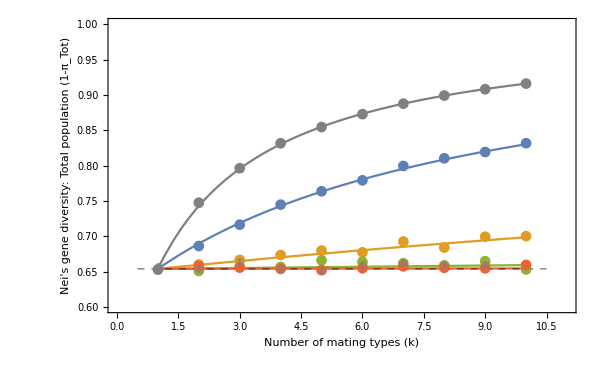

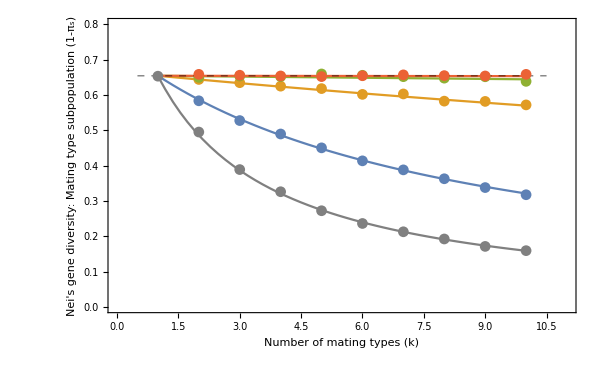

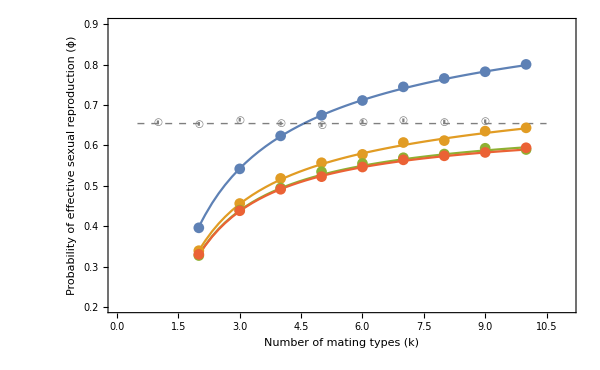

```mathematica
Needs["ErrorBarPlots`"];
params={NT->7560,μB->0.00025,c->5,d->1/2};
σBparams={{σB->0.001},{σB->0.01},{σB->0.1},{σB->1}};

figMonoNeiT=Show[
Plot[Evaluate[1-πTotSI/.σμTrans/.params/.σBparams],{k,1,10},PlotRange->{{0,11},{0.6,1}},
Frame->True,ImageSize->600,FrameStyle->18,FrameLabel->{"Number of mating types (k)","Nei's gene diversity:
Total population (1-π_Tot)"},
PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[4]]}
],
Plot[1-πTotAsex/.σμTrans/.params,{k,1,10},
PlotStyle->Gray],
Plot[1-πTotUnisex/.σμTrans/.params,{k,0.5,10.5},PlotStyle->{Thick,{Black,Opacity[0.5]},Dashed}],
ErrorListPlot[HKTSISimTableσ],
ErrorListPlot[HKTAsexSimTableσ,PlotStyle->Gray],
ErrorListPlot[HKTUniSimTableσ,PlotMarkers->{Graphics`PlotMarkers[][[6]]},PlotStyle->Gray]
]

figMonoNeiS=Show[
Plot[Evaluate[1-πsSI/.σμTrans/.params/.σBparams],{k,1,10},PlotRange->{{0,11},{0,0.8}},
Frame->True,ImageSize->600,FrameStyle->18,FrameLabel->{"Number of mating types (k)","Nei's gene diversity:
Mating type subpopulation (1-π_s)"},
PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[4]]}
],
Plot[1-πsAsex/.σμTrans/.params,{k,1,10},
PlotStyle->Gray],
Plot[1-πTotUnisex/.σμTrans/.params,{k,0.5,10.5},
PlotStyle->{Thick,{Black,Opacity[0.5]},Dashed}],
ErrorListPlot[HKSSISimTableσ],
ErrorListPlot[HKSAsexSimTableσ,PlotStyle->Gray]
]

figMonoϕ=Show[
Plot[Evaluate[ϕSI/.σμTrans/.params/.σBparams],{k,2,10},PlotRange->{{0,11},{0.2,0.9}},
Frame->True,ImageSize->600,FrameStyle->18,FrameLabel->{"Number of mating types (k)","Probability of effective
sexual reproduction (ϕ)"},
PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[4]]}
],
Plot[ϕUnisex/.σμTrans/.params,{k,0.5,10.5},
PlotStyle->{Thick,{Black,Opacity[0.5]},Dashed}],
ListPlot[Table[N[ϕSISimTableσ][[i]][[All,1]],{i,1,Length[ϕSISimTableσ]}]],
ErrorListPlot[HKTUniSimTableσ,PlotMarkers->{Graphics`PlotMarkers[][[6]]},PlotStyle->Gray]
]

figMonoLeg=
LineLegend[
Join[{Directive[Gray]},Flatten[Table[{Directive[ColorData[97,"ColorList"][[i]]]},{i,1,4}]],{Directive[Gray,Dashed]}],
Join[{Style["σ^-=0 (k demes)",18]},Flatten[Table[{Style["σ^-="<>ToString[σB/.σBparams[[i]]],18]},{i,1,4}]],{Style["σ^-∈[0,1]",18]}]
]
```

### Mixed population of Unisexuals and k-1 Self-incompatible types: ϕ (Figure 8)

#### Load Mixed pop results: α=0.25

```mathematica
Needs["ErrorBarPlots`"]
params={NT->7560,μB->0.00025,c->5,d->1/2,α->0.25};
σBparams={{σB->0.001},{σB->0.01},{σB->0.1},{σB->1}};
σBparams={{σB->0.001},{σB->0.01},{σB->0.1}};

kParams=Table[{k->i},{i,2,10}];

(* π = prob IBM *)
(* πsSI = prob IBM - two individuals from same SI class (not needed here) *)
(* πdSI = prob IBM - two individuals from different SI classes *)
(* πsU = prob IBM - two individuals from U class *)
(* πdU = prob IBM - one individual from U, one from SI class *)

πdSITableσ=ConstantArray[0,Length[σBparams] ];
πsUTableσ=ConstantArray[0,Length[σBparams] ];
πdUTableσ=ConstantArray[0,Length[σBparams] ];

ϕMixedSimTableσU=ConstantArray[0,Length[σBparams] ];
ϕMixedSimTableσS=ConstantArray[0,Length[σBparams] ];

For[jσ=1,jσ≤Length[σBparams],jσ++,

πdSITable=Table[{{i,0},0},{i,2,10}];
πsUTable=Table[{{i,0},0},{i,2,10}];
πdUTable=Table[{{i,0},0},{i,2,10}];


ϕMixedSimTableU=Table[{{i,0},0},{i,2,10}];
ϕMixedSimTableS=Table[{{i,0},0},{i,2,10}];

(* Loop over different k values *)
For[j=1,j≤Length[kParams],j++,

Print["σ= "<>ToString[N[σB/.σBparams[[jσ]]]]<>" . K="<>ToString[N[k/.params/.kParams[[j]]]]];

traj=Import[NotebookDirectory[]<>"Data/MixedPopData/alph_"<>ToString[α/.params]<>"_sigB_"<>ToString[σB/.σBparams[[jσ]]]<>"_c_"<>ToString[c/.params]<>"_muB_"<>ToString[μB/.params]<>"_k_"<>ToString[k/.kParams[[j]]]<>"_N_"<>ToString[NT/.params]<>"_mint_100000_maxt_1.01e+07_dt_10000.txt","Table"];


(* Initialise π's value for that k *)
πdSITrajTable=ConstantArray[0,Length[traj]];
πsUTrajTable=ConstantArray[0,Length[traj]];
πdUTrajTable=ConstantArray[0,Length[traj]];

NU=Floor[NT*α/.params];
NSI=Floor[(NT*(1-α))/(k-1)/.params/.kParams[[j]]];

Print["σ= "<>ToString[N[σB/.σBparams[[jσ]]]]<>" . K="<>ToString[N[k/.params/.kParams[[j]]]]<>" . N="<>ToString[N[NT/.params]]<>" . NU="<>ToString[N[NU]]<>" . NSI="<>ToString[N[NSI]]];

(* Loop over time samples *)
For[i=1,i≤Length[traj],i++,
trajTrunc=traj[[i,2;;]];

(* Consider πsU first (prob IBD two individuals from U class) *)

(* Seperate out focal and remainder types *)
focalMT=trajTrunc[[1;;NU]];
(* For unisex type, remainder MT is entire population *)
remainderMT=trajTrunc[[1;;NU]];
(* Work out which alleles they have in common *)
intersectionList=Intersection[focalMT,remainderMT];
(* Loop over alleles in common, working out the respective probability of picking each *)
For[m=1,m≤Length[intersectionList],m++,
πsUTrajTable[[i]]=πsUTrajTable[[i]]+(Count[focalMT,intersectionList[[m]]]/NU*Count[remainderMT,intersectionList[[m]]]/NU)/.params/.kParams[[j]];
];

(* Consider πdU second (prob IBD one individual from U class, one from SI class) *)

(* Seperate out focal and remainder types *)
focalMT=trajTrunc[[1;;NU]];
(* For unisex type, remainder MT is entire population *)
remainderMT=trajTrunc[[(NU+1);;]];
(* Work out which alleles they have in common *)
intersectionList=Intersection[focalMT,remainderMT];
(* Loop over alleles in common, working out the respective probability of picking each *)
For[m=1,m≤Length[intersectionList],m++,
πdUTrajTable[[i]]=πdUTrajTable[[i]]+(Count[focalMT,intersectionList[[m]]]/NU*Count[remainderMT,intersectionList[[m]]]/((NT-NU)/.params))/.params/.kParams[[j]];
];

(* Consider πdSI last (prob IBD two individuals from different SI classes) *)

(* Loop over remaining mating type classes, comparing each focal type with remainder of population *)
For[l=1,l≤(k-1/.kParams[[j]]),l++,
(* Seperate out focal and remainder types *)
focalMT=trajTrunc[[(NU+(l-1)*NSI+1);;(NU+(l)*NSI)]];

remainderMT=Join[trajTrunc[[NU+1;;(NU+(l-1)*NSI)]],trajTrunc[[(NU+(l)*NSI+1);;]]];
(* Work out which alleles they have in common *)
intersectionList=Intersection[focalMT,remainderMT];
(* Loop over alleles in common, working out the respective probability of picking each *)
For[m=1,m≤Length[intersectionList],m++,
πdSITrajTable[[i]]=πdSITrajTable[[i]]+1/(k-1)(Count[focalMT,intersectionList[[m]]]/NSI*Count[remainderMT,intersectionList[[m]]]/(NT-NSI-NU/.params))/.params/.kParams[[j]];
];
];
];

πdSITable[[j,1]][[2]]=Mean[πdSITrajTable];
πsUTable[[j,1]][[2]]=Mean[πsUTrajTable];
πdUTable[[j,1]][[2]]=Mean[πdUTrajTable];

πdSITable[[j,2]]=ErrorBar[StandardDeviation[πdSITrajTable]/(√Length[traj])];
πsUTable[[j,2]]=ErrorBar[StandardDeviation[πsUTrajTable]/(√Length[traj])];
πdUTable[[j,2]]=ErrorBar[StandardDeviation[πdUTrajTable]/(√Length[traj])];


ϕMixedSimTableS[[j,1]][[2]]=Mean[N[(k-2)1/(1-Exp[-c]pi)pj(1-πdSITrajTable)+1/(1-Exp[-c]pi)pu(1-πdUTrajTable)/.{pi->(1-α)/(k-1),pj->(1-α)/(k-1),pu->α}/.params/.kParams[[j]]]];
ϕMixedSimTableU[[j,1]][[2]]=Mean[N[(k-1)pj(1-πdUTrajTable)+pu(1-πsUTrajTable)/.{pj->(1-α)/(k-1),pu->α}/.params/.kParams[[j]]]];

ϕMixedSimTableS[[j,2]]=ErrorBar[1/(√Length[traj])StandardDeviation[N[(k-2)1/(1-Exp[-c]pi)pj(1-πdSITrajTable)+1/(1-Exp[-c]pi)pu(1-πdUTrajTable)/.{pi->(1-α)/(k-1),pj->(1-α)/(k-1),pu->α}/.params/.kParams[[j]]]]];
ϕMixedSimTableU[[j,2]]=ErrorBar[1/(√Length[traj])StandardDeviation[N[(k-1)pj(1-πdUTrajTable)+pu(1-πsUTrajTable)/.{pj->(1-α)/(k-1),pu->α}/.params/.kParams[[j]]]]];

];

πdSITableσ[[jσ]]=πdSITable;
πsUTableσ[[jσ]]=πsUTable;
πdUTableσ[[jσ]]=πdUTable;

ϕMixedSimTableσU[[jσ]]=ϕMixedSimTableU;
ϕMixedSimTableσS[[jσ]]=ϕMixedSimTableS;

];

ϕMixedSimTableσU025=ϕMixedSimTableσU;
ϕMixedSimTableσS025=ϕMixedSimTableσS;
```

σ= 0.001 . K=2.

σ= 0.001 . K=2. . N=7560. . NU=1890. . NSI=5670.

σ= 0.001 . K=3.

σ= 0.001 . K=3. . N=7560. . NU=1890. . NSI=2835.

σ= 0.001 . K=4.

σ= 0.001 . K=4. . N=7560. . NU=1890. . NSI=1890.

σ= 0.001 . K=5.

σ= 0.001 . K=5. . N=7560. . NU=1890. . NSI=1417.

σ= 0.001 . K=6.

σ= 0.001 . K=6. . N=7560. . NU=1890. . NSI=1134.

σ= 0.001 . K=7.

σ= 0.001 . K=7. . N=7560. . NU=1890. . NSI=945.

σ= 0.001 . K=8.

σ= 0.001 . K=8. . N=7560. . NU=1890. . NSI=810.

σ= 0.001 . K=9.

σ= 0.001 . K=9. . N=7560. . NU=1890. . NSI=708.

σ= 0.001 . K=10.

σ= 0.001 . K=10. . N=7560. . NU=1890. . NSI=630.

σ= 0.01 . K=2.

σ= 0.01 . K=2. . N=7560. . NU=1890. . NSI=5670.

σ= 0.01 . K=3.

σ= 0.01 . K=3. . N=7560. . NU=1890. . NSI=2835.

σ= 0.01 . K=4.

σ= 0.01 . K=4. . N=7560. . NU=1890. . NSI=1890.

σ= 0.01 . K=5.

σ= 0.01 . K=5. . N=7560. . NU=1890. . NSI=1417.

σ= 0.01 . K=6.

σ= 0.01 . K=6. . N=7560. . NU=1890. . NSI=1134.

σ= 0.01 . K=7.

σ= 0.01 . K=7. . N=7560. . NU=1890. . NSI=945.

σ= 0.01 . K=8.

σ= 0.01 . K=8. . N=7560. . NU=1890. . NSI=810.

σ= 0.01 . K=9.

σ= 0.01 . K=9. . N=7560. . NU=1890. . NSI=708.

σ= 0.01 . K=10.

σ= 0.01 . K=10. . N=7560. . NU=1890. . NSI=630.

σ= 0.1 . K=2.

σ= 0.1 . K=2. . N=7560. . NU=1890. . NSI=5670.

σ= 0.1 . K=3.

σ= 0.1 . K=3. . N=7560. . NU=1890. . NSI=2835.

σ= 0.1 . K=4.

σ= 0.1 . K=4. . N=7560. . NU=1890. . NSI=1890.

σ= 0.1 . K=5.

σ= 0.1 . K=5. . N=7560. . NU=1890. . NSI=1417.

σ= 0.1 . K=6.

σ= 0.1 . K=6. . N=7560. . NU=1890. . NSI=1134.

σ= 0.1 . K=7.

σ= 0.1 . K=7. . N=7560. . NU=1890. . NSI=945.

σ= 0.1 . K=8.

σ= 0.1 . K=8. . N=7560. . NU=1890. . NSI=810.

σ= 0.1 . K=9.

σ= 0.1 . K=9. . N=7560. . NU=1890. . NSI=708.

σ= 0.1 . K=10.

σ= 0.1 . K=10. . N=7560. . NU=1890. . NSI=630.

#### Load Mixed pop results: α=0.75

```mathematica
Needs["ErrorBarPlots`"]
params={NT->7560,μB->0.00025,c->5,d->1/2,α->0.75};
σBparams={{σB->0.001},{σB->0.01},{σB->0.1},{σB->1}};
σBparams={{σB->0.001},{σB->0.01},{σB->0.1}};

kParams=Table[{k->i},{i,2,10}];

(* π = prob IBM *)
(* πsSI = prob IBM - two individuals from same SI class (not needed here) *)
(* πdSI = prob IBM - two individuals from different SI classes *)
(* πsU = prob IBM - two individuals from U class *)
(* πdU = prob IBM - one individual from U, one from SI class *)

πdSITableσ=ConstantArray[0,Length[σBparams] ];
πsUTableσ=ConstantArray[0,Length[σBparams] ];
πdUTableσ=ConstantArray[0,Length[σBparams] ];

ϕMixedSimTableσU=ConstantArray[0,Length[σBparams] ];
ϕMixedSimTableσS=ConstantArray[0,Length[σBparams] ];

For[jσ=1,jσ≤Length[σBparams],jσ++,

πdSITable=Table[{{i,0},0},{i,2,10}];
πsUTable=Table[{{i,0},0},{i,2,10}];
πdUTable=Table[{{i,0},0},{i,2,10}];

ϕMixedSimTableU=Table[{{i,0},0},{i,2,10}];
ϕMixedSimTableS=Table[{{i,0},0},{i,2,10}];

(* Loop over different k values *)
For[j=1,j≤Length[kParams],j++,

Print["σ= "<>ToString[N[σB/.σBparams[[jσ]]]]<>" . K="<>ToString[N[k/.params/.kParams[[j]]]]];

traj=Import[NotebookDirectory[]<>"Data/MixedPopData/alph_"<>ToString[α/.params]<>"_sigB_"<>ToString[σB/.σBparams[[jσ]]]<>"_c_"<>ToString[c/.params]<>"_muB_"<>ToString[μB/.params]<>"_k_"<>ToString[k/.kParams[[j]]]<>"_N_"<>ToString[NT/.params]<>"_mint_100000_maxt_1.01e+07_dt_10000.txt","Table"];


(* Initialise π's value for that k *)
πdSITrajTable=ConstantArray[0,Length[traj]];
πsUTrajTable=ConstantArray[0,Length[traj]];
πdUTrajTable=ConstantArray[0,Length[traj]];


NU=Floor[NT*α/.params];
NSI=Floor[(NT*(1-α))/(k-1)/.params/.kParams[[j]]];

Print["σ= "<>ToString[N[σB/.σBparams[[jσ]]]]<>" . K="<>ToString[N[k/.params/.kParams[[j]]]]<>" . N="<>ToString[N[NT/.params]]<>" . NU="<>ToString[N[NU]]<>" . NSI="<>ToString[N[NSI]]];

(* Loop over time samples *)
For[i=1,i≤Length[traj],i++,
trajTrunc=traj[[i,2;;]];

(* Consider πsU first (prob IBD two individuals from U class) *)

(* Seperate out focal and remainder types *)
focalMT=trajTrunc[[1;;NU]];
(* For unisex type, remainder MT is entire population *)
remainderMT=trajTrunc[[1;;NU]];
(* Work out which alleles they have in common *)
intersectionList=Intersection[focalMT,remainderMT];
(* Loop over alleles in common, working out the respective probability of picking each *)
For[m=1,m≤Length[intersectionList],m++,
πsUTrajTable[[i]]=πsUTrajTable[[i]]+(Count[focalMT,intersectionList[[m]]]/NU*Count[remainderMT,intersectionList[[m]]]/NU)/.params/.kParams[[j]];
];

(* Consider πdU second (prob IBD one individual from U class, one from SI class) *)

(* Seperate out focal and remainder types *)
focalMT=trajTrunc[[1;;NU]];
(* For unisex type, remainder MT is entire population *)
remainderMT=trajTrunc[[(NU+1);;]];
(* Work out which alleles they have in common *)
intersectionList=Intersection[focalMT,remainderMT];
(* Loop over alleles in common, working out the respective probability of picking each *)
For[m=1,m≤Length[intersectionList],m++,
πdUTrajTable[[i]]=πdUTrajTable[[i]]+(Count[focalMT,intersectionList[[m]]]/NU*Count[remainderMT,intersectionList[[m]]]/((NT-NU)/.params))/.params/.kParams[[j]];
];

(* Consider πdSI last (prob IBD two individuals from different SI classes) *)

(* Loop over remaining mating type classes, comparing each focal type with remainder of population *)
For[l=1,l≤(k-1/.kParams[[j]]),l++,
(* Seperate out focal and remainder types *)
focalMT=trajTrunc[[(NU+(l-1)*NSI+1);;(NU+(l)*NSI)]];
(*remainderMT=trajTrunc[[(1+l*NK/.params);;]];*)
remainderMT=Join[trajTrunc[[NU+1;;(NU+(l-1)*NSI)]],trajTrunc[[(NU+(l)*NSI+1);;]]];
(* Work out which alleles they have in common *)
intersectionList=Intersection[focalMT,remainderMT];
(* Loop over alleles in common, working out the respective probability of picking each *)
For[m=1,m≤Length[intersectionList],m++,
πdSITrajTable[[i]]=πdSITrajTable[[i]]+1/(k-1)(Count[focalMT,intersectionList[[m]]]/NSI*Count[remainderMT,intersectionList[[m]]]/(NT-NSI-NU/.params))/.params/.kParams[[j]];
];
];
];

πdSITable[[j,1]][[2]]=Mean[πdSITrajTable];
πsUTable[[j,1]][[2]]=Mean[πsUTrajTable];
πdUTable[[j,1]][[2]]=Mean[πdUTrajTable];

πdSITable[[j,2]]=ErrorBar[StandardDeviation[πdSITrajTable]/(√Length[traj])];
πsUTable[[j,2]]=ErrorBar[StandardDeviation[πsUTrajTable]/(√Length[traj])];
πdUTable[[j,2]]=ErrorBar[StandardDeviation[πdUTrajTable]/(√Length[traj])];

ϕMixedSimTableS[[j,1]][[2]]=Mean[N[(k-2)1/(1-Exp[-c]pi)pj(1-πdSITrajTable)+1/(1-Exp[-c]pi)pu(1-πdUTrajTable)/.{pi->(1-α)/(k-1),pj->(1-α)/(k-1),pu->α}/.params/.kParams[[j]]]];
ϕMixedSimTableU[[j,1]][[2]]=Mean[N[(k-1)pj(1-πdUTrajTable)+pu(1-πsUTrajTable)/.{pj->(1-α)/(k-1),pu->α}/.params/.kParams[[j]]]];

ϕMixedSimTableS[[j,2]]=ErrorBar[1/(√Length[traj])StandardDeviation[N[(k-2)1/(1-Exp[-c]pi)pj(1-πdSITrajTable)+1/(1-Exp[-c]pi)pu(1-πdUTrajTable)/.{pi->(1-α)/(k-1),pj->(1-α)/(k-1),pu->α}/.params/.kParams[[j]]]]];
ϕMixedSimTableU[[j,2]]=ErrorBar[1/(√Length[traj])StandardDeviation[N[(k-1)pj(1-πdUTrajTable)+pu(1-πsUTrajTable)/.{pj->(1-α)/(k-1),pu->α}/.params/.kParams[[j]]]]];

];

πdSITableσ[[jσ]]=πdSITable;
πsUTableσ[[jσ]]=πsUTable;
πdUTableσ[[jσ]]=πdUTable;

ϕMixedSimTableσU[[jσ]]=ϕMixedSimTableU;
ϕMixedSimTableσS[[jσ]]=ϕMixedSimTableS;

];


ϕMixedSimTableσU075=ϕMixedSimTableσU;
ϕMixedSimTableσS075=ϕMixedSimTableσS;
```

σ= 0.001 . K=2.

σ= 0.001 . K=2. . N=7560. . NU=5670. . NSI=1890.

σ= 0.001 . K=3.

σ= 0.001 . K=3. . N=7560. . NU=5670. . NSI=945.

σ= 0.001 . K=4.

σ= 0.001 . K=4. . N=7560. . NU=5670. . NSI=630.

σ= 0.001 . K=5.

σ= 0.001 . K=5. . N=7560. . NU=5670. . NSI=472.

σ= 0.001 . K=6.

σ= 0.001 . K=6. . N=7560. . NU=5670. . NSI=378.

σ= 0.001 . K=7.

σ= 0.001 . K=7. . N=7560. . NU=5670. . NSI=315.

σ= 0.001 . K=8.

σ= 0.001 . K=8. . N=7560. . NU=5670. . NSI=270.

σ= 0.001 . K=9.

σ= 0.001 . K=9. . N=7560. . NU=5670. . NSI=236.

σ= 0.001 . K=10.

σ= 0.001 . K=10. . N=7560. . NU=5670. . NSI=210.

σ= 0.01 . K=2.

σ= 0.01 . K=2. . N=7560. . NU=5670. . NSI=1890.

σ= 0.01 . K=3.

σ= 0.01 . K=3. . N=7560. . NU=5670. . NSI=945.

σ= 0.01 . K=4.

σ= 0.01 . K=4. . N=7560. . NU=5670. . NSI=630.

σ= 0.01 . K=5.

σ= 0.01 . K=5. . N=7560. . NU=5670. . NSI=472.

σ= 0.01 . K=6.

σ= 0.01 . K=6. . N=7560. . NU=5670. . NSI=378.

σ= 0.01 . K=7.

σ= 0.01 . K=7. . N=7560. . NU=5670. . NSI=315.

σ= 0.01 . K=8.

σ= 0.01 . K=8. . N=7560. . NU=5670. . NSI=270.

σ= 0.01 . K=9.

σ= 0.01 . K=9. . N=7560. . NU=5670. . NSI=236.

σ= 0.01 . K=10.

σ= 0.01 . K=10. . N=7560. . NU=5670. . NSI=210.

σ= 0.1 . K=2.

σ= 0.1 . K=2. . N=7560. . NU=5670. . NSI=1890.

σ= 0.1 . K=3.

σ= 0.1 . K=3. . N=7560. . NU=5670. . NSI=945.

σ= 0.1 . K=4.

σ= 0.1 . K=4. . N=7560. . NU=5670. . NSI=630.

σ= 0.1 . K=5.

σ= 0.1 . K=5. . N=7560. . NU=5670. . NSI=472.

σ= 0.1 . K=6.

σ= 0.1 . K=6. . N=7560. . NU=5670. . NSI=378.

σ= 0.1 . K=7.

σ= 0.1 . K=7. . N=7560. . NU=5670. . NSI=315.

σ= 0.1 . K=8.

σ= 0.1 . K=8. . N=7560. . NU=5670. . NSI=270.

σ= 0.1 . K=9.

σ= 0.1 . K=9. . N=7560. . NU=5670. . NSI=236.

σ= 0.1 . K=10.

σ= 0.1 . K=10. . N=7560. . NU=5670. . NSI=210.

#### Style plots for export

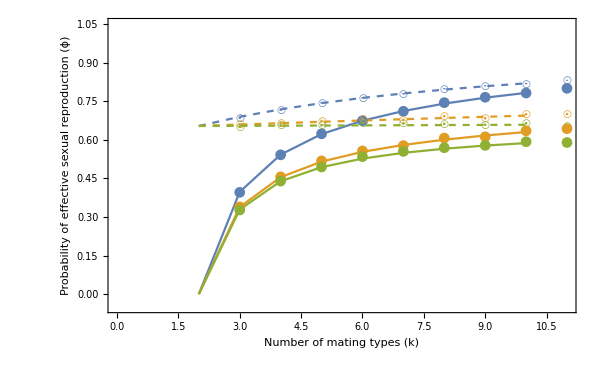

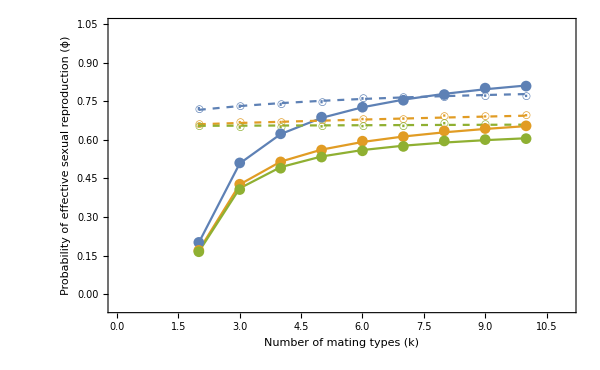

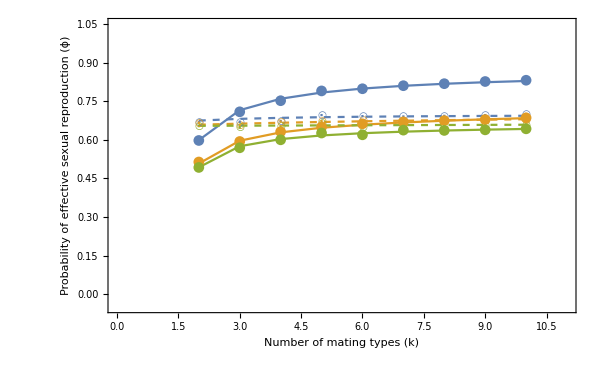

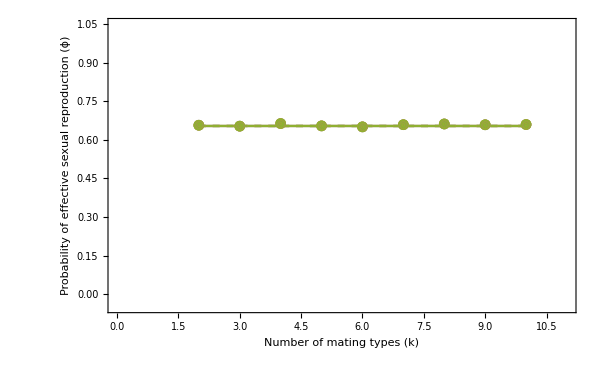

```mathematica
σBparams={{σB->0.001},{σB->0.01},{σB->0.1}};
plotFrames={
Show[
ListLinePlot[Table[{k,ϕMixedSI[0.25,k]/.σμTrans/.params},{k,2,10}]/.σBparams,PlotRange->{{0,11},{-0.05,1.05}},Frame->True,ImageSize->600,FrameStyle->18,FrameLabel->{"Number of mating types (k)","Probability of effective
sexual reproduction (ϕ)"}],
ListLinePlot[Table[{k,ϕMixedU[0.25,k]/.σμTrans/.params},{k,2,10}]/.σBparams,PlotRange->All,PlotStyle->Dashed],
ErrorListPlot[ϕMixedSimTableσU025,PlotMarkers->{Graphics`PlotMarkers[][[6]]}],
ErrorListPlot[ϕMixedSimTableσS025]
],
Show[
ListLinePlot[Table[{k,ϕMixedSI[0.75,k]/.σμTrans/.params},{k,2,10}]/.σBparams,PlotRange->{{0,11},{-0.05,1.05}},Frame->True,ImageSize->600,FrameStyle->18,FrameLabel->{"Number of mating types (k)","Probability of effective
sexual reproduction (ϕ)"}],
ListLinePlot[Table[{k,ϕMixedU[0.75,k]/.σμTrans/.params},{k,2,10}]/.σBparams,PlotRange->All,PlotStyle->Dashed],
ErrorListPlot[ϕMixedSimTableσU075,PlotMarkers->{Graphics`PlotMarkers[][[6]]}],
ErrorListPlot[ϕMixedSimTableσS075]
]
};

(* Modify monomorphic population sims for invasion conditions *)

ϕSISimTableUInvσ=ϕSISimTableσ[[1;;3]];
For[j=1,j≤Length[ϕSISimTableUInvσ],j++,
For[i=1,i≤Length[ϕSISimTableUInvσ[[j]]],i++,ϕSISimTableUInvσ[[j]][[i,1]][[1]]=ϕSISimTableσ[[j]][[i,1]][[1]]+1];
];

ϕUSimTableUInvσ=HKTSISimTableσ[[1;;3]];
For[j=1,j≤Length[ϕUSimTableUInvσ],j++,
For[i=1,i≤Length[ϕUSimTableUInvσ[[j]]],i++,
ϕUSimTableUInvσ[[j]][[i,1]][[1]]=ϕUSimTableUInvσ[[j]][[i,1]][[1]]+1;
ϕUSimTableUInvσ[[j]][[i,2]][[1]]=ϕUSimTableUInvσ[[j]][[i,2]][[1]];
];
];

ϕSISimTableSIInvσ=Table[Flatten[HKTUniSimTableσ,1],{i,1,3}];
ϕUSimTableSIInvσ=Table[Flatten[HKTUniSimTableσ,1],{i,1,3}];

For[j=1,j≤Length[ϕSISimTableSIInvσ],j++,
For[i=1,i≤Length[ϕSISimTableSIInvσ[[j]]],i++,
ϕSISimTableSIInvσ[[j]][[i,1]][[1]]=ϕSISimTableSIInvσ[[j]][[i,1]][[1]]+1;
ϕUSimTableSIInvσ[[j]][[i,1]][[1]]=ϕUSimTableSIInvσ[[j]][[i,1]][[1]]+1;
];
];



plotFrames=Join[
{
Show[
ListLinePlot[Table[{k,ϕUInvSI/.σμTrans/.params},{k,2,10}]/.σBparams,PlotRange->{{0,11},{-0.05,1.05}},Frame->True,ImageSize->600,FrameStyle->18,FrameLabel->{"Number of mating types (k)","Probability of effective
sexual reproduction (ϕ)"}],
ListLinePlot[Table[{k,ϕUInvU/.σμTrans/.params},{k,2,10}]/.σBparams,PlotStyle->Dashed],
ErrorListPlot[ϕSISimTableUInvσ],
ErrorListPlot[ϕUSimTableUInvσ,PlotMarkers->{Graphics`PlotMarkers[][[6]]}]
]
},
plotFrames,
{
Show[
ListLinePlot[Table[{k,ϕUnisex/.σμTrans/.params},{k,2,10}]/.σBparams,PlotRange->{{0,11},{-0.05,1.05}},Frame->True,ImageSize->600,FrameStyle->18,FrameLabel->{"Number of mating types (k)","Probability of effective
sexual reproduction (ϕ)"}],
ListLinePlot[Table[{k,ϕUnisex/.σμTrans/.params},{k,2,10}]/.σBparams,PlotRange->All,PlotStyle->Dashed],
ErrorListPlot[ϕSISimTableSIInvσ],
ErrorListPlot[ϕUSimTableSIInvσ,PlotMarkers->{Graphics`PlotMarkers[][[6]]}]
]
}
];

plotFrames[[1]]
plotFrames[[2]]
plotFrames[[3]]
plotFrames[[4]]

figMixedLeg=LineLegend[
Join[Flatten[Table[{Directive[ColorData[97,"ColorList"][[i]]]},{i,1,3}]],
Flatten[Table[{Directive[ColorData[97,"ColorList"][[i]],Dashed]},{i,1,3}]]],
Join[Flatten[Table[{Style["σ^-="<>ToString[σB/.σBparams[[i]]]<>" (SI)",18]},{i,1,3}]],
Flatten[Table[{Style["σ^-="<>ToString[σB/.σBparams[[i]]]<>" (Unisex)",18]},{i,1,3}]]]
]
```

## Plot 7

#### ϕSI/ϕU 2

{k→2,d→1/2,NT→10000,μB→1/1000000000}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

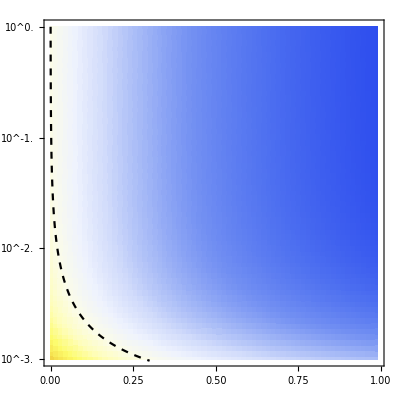

```mathematica
σμTrans={σ->σB*NT,μ->μB*NT};
params={k->2,d->1/2,NT->10^4,μB->10^-9}
trialData=Flatten[Table[{j,-i,ϕSI/ϕUnisex/.σμTrans/.params/.{σB->10^-i,c->j}},{i,0,3,0.05},{j,0,1,0.015}],1];
barMinMax={1-(Max[Abs[trialData[[All,3]]-1]]),1+(Max[Abs[trialData[[All,3]]-1]])};

PlotA=Show[
ListDensityPlot[trialData,InterpolationOrder->0,PlotRange->{Automatic,Automatic,barMinMax},
ColorFunctionScaling->False,ColorFunction->((ColorData["TemperatureMap"])[Rescale[#,barMinMax]]&),
FrameTicks->{{Table[{-i,If[Mod[i,1]==0,Superscript[10,-i],""]},{i,0,3,0.2}],Automatic},{Automatic,Automatic}},FrameStyle->14
],
Plot[Log10[σB/.Solve[(ϕSI/ϕUnisex/.σμTrans/.params)==1,σB][[1]]],{c,0,0.3},PlotRange->All,PlotStyle->{Black,Dashed}]
]

plotAleg=BarLegend[{((ColorData["LightTemperatureMap"])[Rescale[#,barMinMax]]&),barMinMax},LegendMarkerSize->350,LabelStyle->16,LegendLayout->"Column",
TicksStyle->18,ImageSize->800(*,LegendLabel->Style["ϕ_s/ϕ_u",20]*)]
```

{k→2,d→1/2,NT→1000000,μB→1/1000000000}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

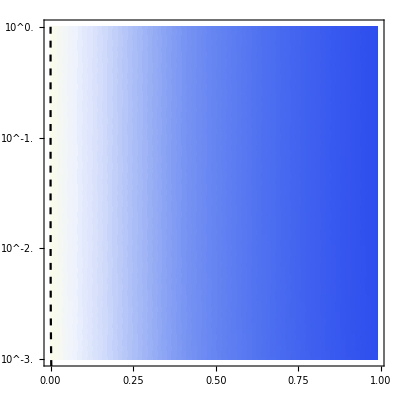

```mathematica
params={k->2,d->1/2,NT->10^6,μB->10^-9}
trialData=Flatten[Table[{j,-i,ϕSI/ϕUnisex/.σμTrans/.params/.{σB->10^-i,c->j}},{i,0,3,0.05},{j,0,1,0.015}],1];
barMinMax={1-(Max[Abs[trialData[[All,3]]-1]]),1+(Max[Abs[trialData[[All,3]]-1]])};

PlotB=Show[
ListDensityPlot[trialData,InterpolationOrder->0,PlotRange->{Automatic,Automatic,barMinMax},
ColorFunctionScaling->False,ColorFunction->((ColorData["TemperatureMap"])[Rescale[#,barMinMax]]&),
FrameTicks->{{Table[{-i,If[Mod[i,1]==0,Superscript[10,-i],""]},{i,0,3,0.2}],Automatic},{Automatic,Automatic}},FrameStyle->14
],
Plot[Log10[σB/.Solve[(ϕSI/ϕUnisex/.σμTrans/.params)==1,σB][[1]]],{c,0,0.3},PlotRange->All,PlotStyle->{Black,Dashed}]
]

plotBleg=BarLegend[{((ColorData["LightTemperatureMap"])[Rescale[#,barMinMax]]&),barMinMax},LegendMarkerSize->350,LabelStyle->16,LegendLayout->"Column",
TicksStyle->18,ImageSize->800(*,LegendLabel->Style["ϕ_s/ϕ_u",20]*)]
```

{k→10,d→1/2,NT→10000,μB→1/1000000000}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

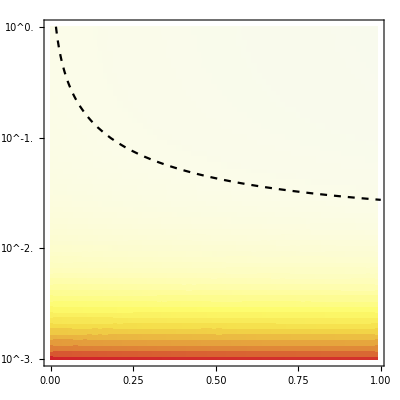

```mathematica
params={k->10,d->1/2,NT->10^4,μB->10^-9}
trialData=Flatten[Table[{j,-i,ϕSI/ϕUnisex/.σμTrans/.params/.{σB->10^-i,c->j}},{i,0,3,0.05},{j,0,1,0.015}],1];
barMinMax={1-(Max[Abs[trialData[[All,3]]-1]]),1+(Max[Abs[trialData[[All,3]]-1]])};

PlotC=Show[
ListDensityPlot[trialData,InterpolationOrder->0,PlotRange->{Automatic,Automatic,barMinMax},
ColorFunctionScaling->False,ColorFunction->((ColorData["TemperatureMap"])[Rescale[#,barMinMax]]&),FrameTicks->{{Table[{-i,If[Mod[i,1]==0,Superscript[10,-i],""]},{i,0,3,0.2}],Automatic},{Automatic,Automatic}},FrameStyle->14
],
Plot[Log10[σB/.Solve[(ϕSI/ϕUnisex/.σμTrans/.params)==1,σB][[1]]],{c,0,1},PlotRange->All,PlotStyle->{Black,Dashed}]
]

plotCleg=BarLegend[{((ColorData["LightTemperatureMap"])[Rescale[#,barMinMax]]&),barMinMax},LegendMarkerSize->350,LabelStyle->16,LegendLayout->"Column",
TicksStyle->18,ImageSize->800(*,LegendLabel->Style["ϕ_s/ϕ_u",20]*)]
```

{k→10,d→1/2,NT→1000000,μB→1/1000000000}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

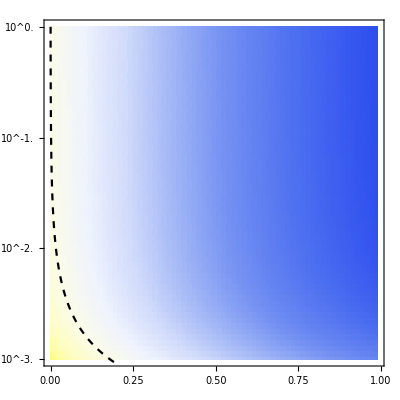

```mathematica
params={k->10,d->1/2,NT->10^6,μB->10^-9}
trialData=Flatten[Table[{j,-i,ϕSI/ϕUnisex/.σμTrans/.params/.{σB->10^-i,c->j}},{i,0,3,0.05},{j,0,1,0.015}],1];
barMinMax={1-(Max[Abs[trialData[[All,3]]-1]]),1+(Max[Abs[trialData[[All,3]]-1]])};

PlotD=Show[
ListDensityPlot[trialData,InterpolationOrder->0,PlotRange->{Automatic,Automatic,barMinMax},
ColorFunctionScaling->False,ColorFunction->((ColorData["TemperatureMap"])[Rescale[#,barMinMax]]&),
FrameTicks->{{Table[{-i,If[Mod[i,1]==0,Superscript[10,-i],""]},{i,0,3,0.2}],Automatic},{Automatic,Automatic}},FrameStyle->14
],
Plot[Log10[σB/.Solve[(ϕSI/ϕUnisex/.σμTrans/.params)==1,σB][[1]]],{c,0,0.2},PlotRange->All,PlotStyle->{Black,Dashed}]
]

plotDleg=BarLegend[{((ColorData["LightTemperatureMap"])[Rescale[#,barMinMax]]&),barMinMax},LegendMarkerSize->350,LabelStyle->16,LegendLayout->"Column",
TicksStyle->18,ImageSize->800]
```